# Notebook for : Cosmic Microwave Background by Ruth Durrer Second Edition

Geoff Cope
University of Utah
                                                                                                             𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
December 18th, 2022

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

```mathematica
Hyperlink["Spin Weighted Spheroidal Harmonics",
"https://bhptoolkit.org/SpinWeightedSpheroidalHarmonics/"]
```

[Spin Weighted Spheroidal Harmonics](https://bhptoolkit.org/SpinWeightedSpheroidalHarmonics/)

## Hyperlink To Book and Related

```mathematica
Hyperlink["The Cosmic Microwave Background by Ruth Durrer 2nd Edition",
"https://www.cambridge.org/core/books/cosmic-microwave-background/BFB2EEB28E56B6682908DE73E6160CFA"]
```

[The Cosmic Microwave Background by Ruth Durrer 2nd Edition](https://www.cambridge.org/core/books/cosmic-microwave-background/BFB2EEB28E56B6682908DE73E6160CFA)

```mathematica
Hyperlink["General Relativity An Introduction for Physicists by Hobson et al Page 288","https://www.cambridge.org/us/academic/subjects/physics/astrophysics/general-relativity-introduction-physicists?format=HB&isbn=9780521829519"]
```

[General Relativity An Introduction for Physicists by Hobson et al Page 288](https://www.cambridge.org/us/academic/subjects/physics/astrophysics/general-relativity-introduction-physicists?format=HB&isbn=9780521829519)

```mathematica
Hyperlink["Introduction to 3+1 Numerical Relativity - Alcubierre",
"https://global.oup.com/academic/product/introduction-to-31-numerical-relativity-9780199656158?cc=us&lang=en&"]
```

[Introduction to 3+1 Numerical Relativity - Alcubierre](https://global.oup.com/academic/product/introduction-to-31-numerical-relativity-9780199656158?cc=us&lang=en&)

```mathematica
(* See Page 15 *) 
Hyperlink["Numerical Relativity - Solving Einstein's Equations on the Computer by Baumgarte & Shapiro",
"https://www.cambridge.org/core/books/numerical-relativity/72D4F6D791BC6F8F9CF87A60FC354D6A"]
```

[Numerical Relativity - Solving Einstein's Equations on the Computer by Baumgarte & Shapiro](https://www.cambridge.org/core/books/numerical-relativity/72D4F6D791BC6F8F9CF87A60FC354D6A)

```mathematica
(* Page 595 *) 
Hyperlink["Relativistic Hydrodynamics",
"https://global.oup.com/academic/product/relativistic-hydrodynamics-9780198807599?cc=us&lang=en&"]
```

[Relativistic Hydrodynamics](https://global.oup.com/academic/product/relativistic-hydrodynamics-9780198807599?cc=us&lang=en&)

```mathematica
(* Add link to code *) 
Hyperlink["Numerical Relativity: Starting from Scratch by Baumgarte & Shapiro",
"https://www.cambridge.org/core/books/numerical-relativity-starting-from-scratch/FB5B832C4ED8EFE65A5834C6D6D4657D"]
```

[Numerical Relativity: Starting from Scratch by Baumgarte & Shapiro](https://www.cambridge.org/core/books/numerical-relativity-starting-from-scratch/FB5B832C4ED8EFE65A5834C6D6D4657D)

```mathematica
Hyperlink["100 Years of General Relativity: Volume 1 Numerical Relativity by Shibata",
"https://www.worldscientific.com/worldscibooks/10.1142/9692"]
```

[100 Years of General Relativity: Volume 1 Numerical Relativity by Shibata](https://www.worldscientific.com/worldscibooks/10.1142/9692)

```mathematica
Hyperlink["3+1 Formalism and Bases of Numerical Relativity - Gourgoulhon",
"https://arxiv.org/abs/gr-qc/0703035"]
```

[3+1 Formalism and Bases of Numerical Relativity - Gourgoulhon](https://arxiv.org/abs/gr-qc/0703035)

```mathematica
Hyperlink["Sebastiano Bernuzzi Numerical Relativity 2021",
"http://sbernuzzi.gitpages.tpi.uni-jena.de/nr/"]
```

[Sebastiano Bernuzzi Numerical Relativity 2021](http://sbernuzzi.gitpages.tpi.uni-jena.de/nr/)

```mathematica
Hyperlink["Colliding Plane Waves by Griffiths - Book","ftp://nozdr.ru/biblio/kolxoz/P/PGr/Griffiths%20J.B.%20Colliding%20plane%20waves%20in%20general%20relativity%20(OUP,%201991)(ISBN%200198532091)(254s)_PGr_.pdf"]
```

[Colliding Plane Waves by Griffiths - Book](ftp://nozdr.ru/biblio/kolxoz/P/PGr/Griffiths%20J.B.%20Colliding%20plane%20waves%20in%20general%20relativity%20(OUP,%201991)(ISBN%200198532091)(254s)_PGr_.pdf)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 23 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,NaturalLanguageProcessingLoader`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

```mathematica
Needs["VariationalMethods`"]
```

## Custom Notation

```mathematica
<<Notation`
```

```mathematica
CreatePalette[{ 
PasteButton[SubPlus[r]] , 
PasteButton[SubMinus[r]] 
}]
```

4628w_shm20FrontEndObject[LinkObject["4628w_shm", 3, 1]]20Untitled-1

```mathematica
(* Go back and use invisible comma *)

CreatePalette[{
PasteButton[Subscript[ρ,m][t]],
PasteButton[Subscript[ρ,r][t]],
PasteButton[Subscript[ρ,Λ][t]],
PasteButton[Subscript[ρ,b][t]],
PasteButton[Subscript[ρ,dm][t]],
PasteButton[Subscript[ρ,r][t]],
PasteButton[Subscript[ρ,γ][t]],
PasteButton[Subscript[ρ,ν][t]] , 
PasteButton[Subscript[ρ,m0][t]],
PasteButton[Subscript[ρ,r0][t]],
PasteButton[Subscript[ρ,Λ0][t]],
PasteButton[Subscript[ρ,m0]],
PasteButton[Subscript[ρ,r0]],
PasteButton[Subscript[ρ,Λ0]]m,
PasteButton[Subscript[ρ,crit]], 
PasteButton[Subscript[ρ,crit0]]
}]
```

4628w_shm21FrontEndObject[LinkObject["4628w_shm", 3, 1]]21Untitled-2

```mathematica
CreatePalette[{
PasteButton[Subscript[Ω,m][t]],
PasteButton[Subscript[Ω,r][t]],
PasteButton[Subscript[Ω,Λ][t]],
PasteButton[Subscript[Ω,k][t]]
}]
```

4628w_shm22FrontEndObject[LinkObject["4628w_shm", 3, 1]]22Untitled-3

```mathematica
(* Go back and use invisible comma *) 

CreatePalette[{
PasteButton[Subscript[H,0]],
PasteButton[Subscript[Ω,m0]],
PasteButton[Subscript[Ω,r0]],
PasteButton[Subscript[Ω,Λ0]] , 
PasteButton[Subscript[Ω,r0]] , 
PasteButton[Subscript[Ω,k0]] , 
PasteButton[Subscript[Ω,b0]],
PasteButton[Subscript[Ω,dm0]],
PasteButton[Subscript[Ω,ν0]]
}]
```

4628w_shm23FrontEndObject[LinkObject["4628w_shm", 3, 1]]23Untitled-4

```mathematica
CreatePalette[{
PasteButton[Subscript[u,x]] , 
PasteButton[Subscript[u,y]] , 
PasteButton[Subscript[u,z]] , 
PasteButton[Subscript[𝓊,x]] , 
PasteButton[Subscript[𝓊,y]] , 
PasteButton[Subscript[𝓊,z]] , 
PasteButton[Superscript[u,1]] , 
PasteButton[Superscript[u,2]], 
PasteButton[Superscript[u,3]], 
PasteButton[Superscript[𝓊,1]], 
PasteButton[Superscript[𝓊,2]] ,
PasteButton[Superscript[𝓊,3]], 
PasteButton[Subscript[γ,v]], 
PasteButton[Subscript[γ,u]], 
PasteButton[Subscript[γ,𝓊]],
PasteButton[Subscript[ψ,u]], 
PasteButton[Subscript[ψ,v]] 
}]
```

4628w_shm24FrontEndObject[LinkObject["4628w_shm", 3, 1]]24Untitled-5

```mathematica
Symbolize[Subscript[u, x]]
Symbolize[Subscript[u, y]]
Symbolize[Subscript[u, z]]
Symbolize[Subscript[𝓊, x]]
Symbolize[Subscript[𝓊, y]]
Symbolize[Subscript[𝓊, z]]
```

```mathematica
CreatePalette[{
PasteButton[Subscript[a,x]] , 
PasteButton[Subscript[a,y]] , 
PasteButton[Subscript[a,z]] , 
PasteButton[Subscript[𝒶,x]] , 
PasteButton[Subscript[𝒶,y]] , 
PasteButton[Subscript[𝒶,z]] 
}]
```

4628w_shm25FrontEndObject[LinkObject["4628w_shm", 3, 1]]25Untitled-6

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[p]-> dp , 
Dt[q]-> dq , 
Dt[r]-> dr , 
Dt[t]-> dt , 
Dt[u]-> du , 
(* Dt[v]-> dv , *) 
 Dt[w]-> dw , 
Dt[x]-> dx , 
Dt[y]-> dy , 
Dt[z]-> dz ,
Dt[𝓇] -> d𝓇 , 
Dt[𝓉] -> d𝓉  , 
Dt[𝓅] -> d𝓅 , 
Dt[𝓆]-> d𝓆 ,
Dt[ψ]-> dψ ,    
 Dt[θ] -> dθ , 
Dt[ϕ] -> dϕ  ,
Dt[η] -> dη  , 
Dt[χ]-> dχ , 
Dt[ρ] -> dρ ,
Dt[φ] -> dφ , 
 Dt[𝓉] -> d𝓉 , 
Dt[𝓍]-> d𝓍 , 
Dt[𝓎]-> d𝓎 , 
Dt[𝓏] -> d𝓏,
Dt[T]-> dT , 
Dt[U]-> dU , 
Dt[V]-> dV ,
Dt[X]-> dX , 
Dt[Y]-> dY , 
Dt[Z]-> dZ , 
Dt[𝓇]-> d𝓇  , 
Dt[Φ]-> dΦ , 
Dt[Subscript[u, x]]-> Subscript[du, x] , 
Dt[Subscript[u, y]]-> Subscript[du, y] , 
Dt[Subscript[u, z]]-> Subscript[du, z] , 
Dt[Subscript[𝓊, x]]-> Subscript[d𝓊, x] , 
Dt[Subscript[𝓊, y]]-> Subscript[d𝓊, y] , 
Dt[Subscript[𝓊, z]]-> Subscript[d𝓊, z]
};
dtReplace // TableForm
```

Dt[p]→dp
Dt[q]→dq
Dt[r]→dr
Dt[t]→dt
Dt[u]→du
Dt[w]→dw
Dt[x]→dx
Dt[y]→dy
Dt[z]→dz
Dt[𝓇]→d𝓇
Dt[𝓉]→d𝓉
Dt[𝓅]→d𝓅
Dt[𝓆]→d𝓆
Dt[ψ]→dψ
Dt[θ]→dθ
Dt[ϕ]→dϕ
Dt[η]→dη
Dt[χ]→dχ
Dt[ρ]→dρ
Dt[φ]→dφ
Dt[𝓉]→d𝓉
Dt[𝓍]→d𝓍
Dt[𝓎]→d𝓎
Dt[𝓏]→d𝓏
Dt[T]→dT
Dt[U]→dU
Dt[V]→dV
Dt[X]→dX
Dt[Y]→dY
Dt[Z]→dZ
Dt[𝓇]→d𝓇
Dt[Φ]→dΦ
Dt[u_x]→du_x
Dt[u_y]→du_y
Dt[u_z]→du_z
Dt[𝓊_x]→d𝓊_x
Dt[𝓊_y]→d𝓊_y
Dt[𝓊_z]→d𝓊_z

```mathematica
M /: Dt[M] = 0 ;  (* Mass of Schwarzschild is constant *) (* We use M for mass and m for null vector *) 
a /: Dt[a] = 0 ;  (* speed of light is constant *)
c /: Dt[c] = 0 ;  (* fixed angular velocity*)
ω /: Dt[ω] = 0 ;
v /: Dt[v] = 0 ;
A /: Dt[A] = 0 ;
B /: Dt[B] = 0 ;
γ /: Dt[γ] = 0 ;
β /: Dt[β] = 0 ;
```

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Chapter 10

```mathematica
Clear[eq10pt1]
eq10pt1 =  { 
ℐ[ω] == (1/π^2)(ω^3/(Exp[ω/T]-1)) , 
4 π f[ω] ==  (1/π^2)(ω^3/(Exp[ω/T]-1)) 
} ;
eq10pt1  // TableForm
```

ℐ[ω]==ω^3/((-1+ⅇ^(ω/T)) π^2)
4 π f[ω]==ω^3/((-1+ⅇ^(ω/T)) π^2)

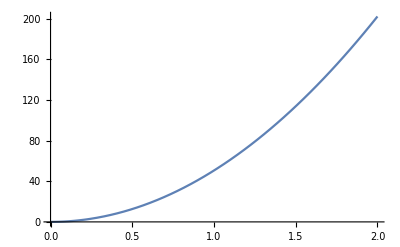

```mathematica
Plot[Evaluate[eq10pt1[[1]][[2]] /. T-> 500],{ω,0,2}]
```

```mathematica
(* Fix this *) 

Clear[eq10pt46]
eq10pt46 = 
∫(x^3/(Exp[x+μ]-1))ⅆx
```

x^3 Log[1-ⅇ^(-x-μ)]-3 x^2 PolyLog[2,ⅇ^(-x-μ)]-6 x PolyLog[3,ⅇ^(-x-μ)]-6 PolyLog[4,ⅇ^(-x-μ)]

```mathematica
(* Fix this *) 

Clear[eq10pt47]
eq10pt47 = 
∫(x^2/(Exp[x+μ]-1))ⅆx
```

x^2 Log[1-ⅇ^(-x-μ)]-2 x PolyLog[2,ⅇ^(-x-μ)]-2 PolyLog[3,ⅇ^(-x-μ)]

```mathematica
(* Fix this *) 

Clear[exercise10pt3]
exercise10pt3 = 
∫_0^1 (1/x)(Exp[x] Exp[-2 xc/x])/(Exp[x]-1)ⅆx
```

∫_0^1 ⅇ^(x-(2 xc)/x)/((-1+ⅇ^x) x)ⅆx

```mathematica
Normal[Series[(1/x)(Exp[x] Exp[-2 xc/x])/(Exp[x]-1) , {x,0,2}]]
```

ⅇ^(x-(2 xc)/x) (1/12+1/x^2-1/(2 x)-x^2/720)

## Appendix A1.1: Conversion Factors, Units (NOT FINISHED) (Attempt to use constants package)

```mathematica
(* Use control = to pull up box *)
```

```mathematica
LinguisticAssistant
```

1 GeV

```mathematica
LinguisticAssistant
```

1 erg

```mathematica
LinguisticAssistant
```

```mathematica
LinguisticAssistant
```

1 g

```mathematica
LinguisticAssistant
```

1 cm

```mathematica
LinguisticAssistant
```

1 s

```mathematica
LinguisticAssistant
```

pc

```mathematica
LinguisticAssistant
```

```mathematica
LinguisticAssistant
```

1 cm

```mathematica
LinguisticAssistant
```

1 M pc

```mathematica
LinguisticAssistant
```

1 cm

```mathematica
LinguisticAssistant
```

1 s

```mathematica
LinguisticAssistant
```

au

```mathematica
LinguisticAssistant
```

1 cm

```mathematica
LinguisticAssistant
```

1 Jy

```mathematica
LinguisticAssistant
```

1 erg

```mathematica
LinguisticAssistant
```

1 Hz

```mathematica
LinguisticAssistant
```

1 GeV

```mathematica
LinguisticAssistant
```

```mathematica
LinguisticAssistant
```

1 rad

```mathematica
LinguisticAssistant
```

1 °

```mathematica
LinguisticAssistant
```

1 sr

## Appendix A1.2.1: Fundamental Constants

```mathematica
LinguisticAssistant
```

h

```mathematica
LinguisticAssistant
```

c

```mathematica
LinguisticAssistant
```

α

```mathematica
LinguisticAssistant
```

G

```mathematica
LinguisticAssistant
```

m_P

```mathematica
LinguisticAssistant
```

l_P

```mathematica
LinguisticAssistant
```

t_P

```mathematica
LinguisticAssistant
```

EntityValue::nodat: Unable to download data. Some or all results may be missing.

Missing[RetrievalFailure]

```mathematica
LinguisticAssistant
```

EntityValue::nodat: Unable to download data. Some or all results may be missing.

Missing[RetrievalFailure]

```mathematica
LinguisticAssistant
```

EntityValue::nodat: Unable to download data. Some or all results may be missing.

Missing[RetrievalFailure]

```mathematica
LinguisticAssistant
```

Johannes Rydberg

```mathematica
LinguisticAssistant
```

σ_t

```mathematica
LinguisticAssistant
```

a_0

```mathematica
LinguisticAssistant
```

μ_B

```mathematica
LinguisticAssistant
```

N_0

```mathematica
LinguisticAssistant
```

N_0

```mathematica
LinguisticAssistant
```

σ

## Appendix A1.2.2: Important Constants

```mathematica
LinguisticAssistant
```

EntityValue::nodat: Unable to download data. Some or all results may be missing.

Missing[RetrievalFailure]

```mathematica
LinguisticAssistant
```

EntityValue::nodat: Unable to download data. Some or all results may be missing.

Missing[RetrievalFailure]

```mathematica
LinguisticAssistant
```

EntityValue::nodat: Unable to download data. Some or all results may be missing.

Missing[RetrievalFailure]

```mathematica
LinguisticAssistant
```

EntityValue::nodat: Unable to download data. Some or all results may be missing.

Missing[RetrievalFailure]

```mathematica
LinguisticAssistant
```

DistanceModulus

```mathematica
LinguisticAssistant
```

H_0

```mathematica
LinguisticAssistant
```

t_H

## Appendix A1.3: Useful Relations (NOT FINISHED)

```mathematica
LinguisticAssistant
```

EntityValue::nodat: Unable to download data. Some or all results may be missing.

Missing[RetrievalFailure]

```mathematica
LinguisticAssistant
```

electron neutrino

## Appendix 4: Special Functions

```mathematica
Clear[P]
P[l_,x_]:= 
LegendreP[l,x]
```

```mathematica
Clear[δ]
δ[i_,j_]:=
 KroneckerDelta[i,j]
```

```mathematica
Clear[A4pt1LHS]
A4pt1LHS[sizeLHS_]:= 
Table[Integrate[ P[l,x] P[m,x] ,{x,-1,1}],{l,1,sizeLHS},{m,1,sizeLHS}]  ;
```

```mathematica
Clear[A4pt1RHS]
A4pt1RHS[sizeRHS_]:= 
Table[ (2/(2l+1)) δ[l,m],{l,1,sizeRHS},{m,1,sizeRHS}]
```

```mathematica
A4pt1LHS[6] // MatrixForm
```

(2/3 | 0 | 0 | 0 | 0 | 0
0 | 2/5 | 0 | 0 | 0 | 0
0 | 0 | 2/7 | 0 | 0 | 0
0 | 0 | 0 | 2/9 | 0 | 0
0 | 0 | 0 | 0 | 2/11 | 0
0 | 0 | 0 | 0 | 0 | 2/13)

```mathematica
A4pt1RHS[6] // MatrixForm
```

(2/3 | 0 | 0 | 0 | 0 | 0
0 | 2/5 | 0 | 0 | 0 | 0
0 | 0 | 2/7 | 0 | 0 | 0
0 | 0 | 0 | 2/9 | 0 | 0
0 | 0 | 0 | 0 | 2/11 | 0
0 | 0 | 0 | 0 | 0 | 2/13)

```mathematica
Thread[Flatten[A4pt1LHS[6]] == Flatten[A4pt1RHS[6]] ]
```

True

```mathematica
Clear[A4pt2]
A4pt2 = 
(l+1) P[l+1,x]==(2 l+1) x P[l,x]-l P[l-1,x]
```

(1+l) LegendreP[1+l,x]==-l LegendreP[-1+l,x]+(1+2 l) x LegendreP[l,x]

```mathematica
A4pt2 // FullSimplify
```

True

```mathematica
Clear[A4pt3]
A4pt3 = 
(1-x^2)Inactivate[D[P[l,x],{x,2}],D]-2x Inactivate[D[P[l,x],x],D]+l (l+1) P[l,x] == 0
```

l (1+l) LegendreP[l,x]-2 x InactiveLegendreP[l,x]x+(1-x^2) InactiveLegendreP[l,x]{x,2}==0

```mathematica
Activate[A4pt3] // Expand // FullSimplify
```

True

```mathematica
Clear[A4pt4]
A4pt4 = 
P[l,x] == 1/(2^l l!)Inactivate[ D[ (x^2-1)^l ,{x, l }],D]
```

LegendreP[l,x]==(2^-l Inactive(-1+x^2)^l{x,l})/(l!)

```mathematica
(* As an example we use l = 5 *) 

A4pt4 /. l-> 5 
A4pt4 /. l-> 5 // Activate
A4pt4 /. l-> 5 // Activate // Expand
```

1/8 (15 x-70 x^3+63 x^5)==(Inactive(-1+x^2)^5{x,5})/3840

1/8 (15 x-70 x^3+63 x^5)==(3840 x^5+19200 x^3 (-1+x^2)+7200 x (-1+x^2)^2)/3840

True

```mathematica
Clear[A4pt5]
A4pt5 = 
Inactivate[LegendreP[0,x]] == P[0,x]
```

LegendreP[0,x]==1

```mathematica
Clear[A4pt6]
A4pt6 = 
Inactivate[LegendreP[1,x]]== P[1,x]
```

LegendreP[1,x]==x

```mathematica
Clear[A4pt7]
A4pt7 = 
Inactivate[LegendreP[2,x]] == P[2,x]
```

LegendreP[2,x]==1/2 (-1+3 x^2)

```mathematica
Clear[A4pt8]
A4pt8 = 
Inactivate[LegendreP[3,x]]== P[3,x]
```

LegendreP[3,x]==1/2 (-3 x+5 x^3)

```mathematica
Clear[A4pt9]
A4pt9= 
Inactivate[LegendreP[4,x]] == P[4,x]
```

LegendreP[4,x]==1/8 (3-30 x^2+35 x^4)

```mathematica
(* we check this for a few values... *) 

Table[(  P[l,-x] == (-1)^l P[l,x] ) /. l-> i , {i,1,10}]
```

{True,True,True,True,True,True,True,True,True,True}

```mathematica
(* Be careful about what is repeated... *) 
(* 
Table[Integrate[LegendreP[l,m,x]LegendreP[ℓ,m,x],{x,-1,1} ],{l,1,6},{ℓ,1,6}] // TableForm
*)
```

```mathematica
?ClebschGordan
```

```mathematica
?ThreeJSymbol
```

```mathematica
?SixJSymbol
```

```mathematica
?SphericalHarmonicY
```

```mathematica
Hyperlink["Spin Weighted Spherical Harmonics",
"https://bhptoolkit.org/SpinWeightedSpheroidalHarmonics/"]
```

[Spin Weighted Spherical Harmonics](https://bhptoolkit.org/SpinWeightedSpheroidalHarmonics/)

```mathematica
?PauliMatrix
```

```mathematica
?BesselJ
```

```mathematica
?SphericalBesselJ
```

```mathematica
?SphericalBesselY
```

```mathematica
?SphericalHankelH1
```

```mathematica
?SphericalHankelH2
```